```mathematica
SetDirectory["C:\\Users\\mi\\CLionProjects\\HorizRK\\cmake-build-debug"]
```

C:\Users\mi\CLionProjects\HorizRK\cmake-build-debug

```mathematica
rk4= Import["rk4.txt","Table"];
eu= Import["euler.txt","Table"];
euMod= Import["euler_mod.txt","Table"];
```

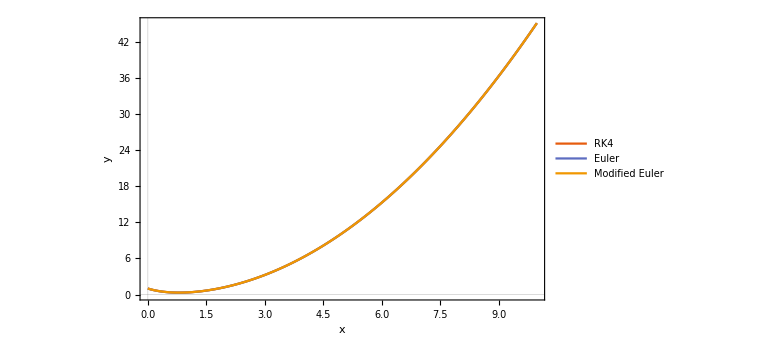

```mathematica
plt=ListLinePlot[{rk4, eu, euMod}, FrameLabel->{"x","y"},PlotRange->Full,ImageSize->Large,PlotTheme->"Scientific",PlotLegends->{"RK4","Euler","Modified Euler"}]
```

```mathematica
Export["plot.png",plt]
```

plot.png